```mathematica
Vt=Vp*Exp[-t^2/(2 wV^2)]
```

ⅇ^(-t^2/(2 wV^2)) Vp

```mathematica
phi=PhiP*(Exp[-(x-x1)^2/(2 wphi^2)]-Exp[-(x-x2)^2/(2 wphi^2)])
```

(ⅇ^(-(x-x1)^2/(2 wphi^2))-ⅇ^(-(x-x2)^2/(2 wphi^2))) PhiP

```mathematica
sfap = InverseFourierTransform[-d^2*omega^2 Pi /(4*v^2)FourierTransform[Vt,t,omega,Assumptions->{wV>0}]*FourierTransform[phi,x,k,Assumptions->{wphi>0}]/.k->(omega/v),omega,t]
```

1/(4 √(1/wphi^2) √(1/wV^2) (wphi^2+v^2 wV^2)^2)d^2 ⅇ^(-(-t v+x1)^2/(2 (wphi^2+v^2 wV^2))-(-t v+x2)^2/(2 (wphi^2+v^2 wV^2))) PhiP π Vp √(v^2/(wphi^2+v^2 wV^2)) (-ⅇ^((-t v+x1)^2/(2 (wphi^2+v^2 wV^2))) t^2 v^2+ⅇ^((-t v+x2)^2/(2 (wphi^2+v^2 wV^2))) t^2 v^2+ⅇ^((-t v+x1)^2/(2 (wphi^2+v^2 wV^2))) wphi^2-ⅇ^((-t v+x2)^2/(2 (wphi^2+v^2 wV^2))) wphi^2+ⅇ^((-t v+x1)^2/(2 (wphi^2+v^2 wV^2))) v^2 wV^2-ⅇ^((-t v+x2)^2/(2 (wphi^2+v^2 wV^2))) v^2 wV^2-2 ⅇ^((-t v+x2)^2/(2 (wphi^2+v^2 wV^2))) t v x1+ⅇ^((-t v+x2)^2/(2 (wphi^2+v^2 wV^2))) x1^2+2 ⅇ^((-t v+x1)^2/(2 (wphi^2+v^2 wV^2))) t v x2-ⅇ^((-t v+x1)^2/(2 (wphi^2+v^2 wV^2))) x2^2) σ

```mathematica
1/(4 √(1/wphi^2) √(1/wV^2) (wphi^2+v^2 wV^2)^2)d^2 ⅇ^(-(-t v+x1)^2/(2 (wphi^2+v^2 wV^2))-(-t v+x2)^2/(2 (wphi^2+v^2 wV^2))) PhiP π Vp √(v^2/(wphi^2+v^2 wV^2)) (-ⅇ^((-t v+x1)^2/(2 (wphi^2+v^2 wV^2))) t^2 v^2+ⅇ^((-t v+x2)^2/(2 (wphi^2+v^2 wV^2))) t^2 v^2+ⅇ^((-t v+x1)^2/(2 (wphi^2+v^2 wV^2))) wphi^2-ⅇ^((-t v+x2)^2/(2 (wphi^2+v^2 wV^2))) wphi^2+ⅇ^((-t v+x1)^2/(2 (wphi^2+v^2 wV^2))) v^2 wV^2-ⅇ^((-t v+x2)^2/(2 (wphi^2+v^2 wV^2))) v^2 wV^2-2 ⅇ^((-t v+x2)^2/(2 (wphi^2+v^2 wV^2))) t v x1+ⅇ^((-t v+x2)^2/(2 (wphi^2+v^2 wV^2))) x1^2+2 ⅇ^((-t v+x1)^2/(2 (wphi^2+v^2 wV^2))) t v x2-ⅇ^((-t v+x1)^2/(2 (wphi^2+v^2 wV^2))) x2^2) σ
sfap = sfap /.v->a*d
```

1/(4 √(1/wphi^2) √(1/wV^2) (wphi^2+v^2 wV^2)^2)d^2 ⅇ^(-(-t v+x1)^2/(2 (wphi^2+v^2 wV^2))-(-t v+x2)^2/(2 (wphi^2+v^2 wV^2))) PhiP π Vp √(v^2/(wphi^2+v^2 wV^2)) (-ⅇ^((-t v+x1)^2/(2 (wphi^2+v^2 wV^2))) t^2 v^2+ⅇ^((-t v+x2)^2/(2 (wphi^2+v^2 wV^2))) t^2 v^2+ⅇ^((-t v+x1)^2/(2 (wphi^2+v^2 wV^2))) wphi^2-ⅇ^((-t v+x2)^2/(2 (wphi^2+v^2 wV^2))) wphi^2+ⅇ^((-t v+x1)^2/(2 (wphi^2+v^2 wV^2))) v^2 wV^2-ⅇ^((-t v+x2)^2/(2 (wphi^2+v^2 wV^2))) v^2 wV^2-2 ⅇ^((-t v+x2)^2/(2 (wphi^2+v^2 wV^2))) t v x1+ⅇ^((-t v+x2)^2/(2 (wphi^2+v^2 wV^2))) x1^2+2 ⅇ^((-t v+x1)^2/(2 (wphi^2+v^2 wV^2))) t v x2-ⅇ^((-t v+x1)^2/(2 (wphi^2+v^2 wV^2))) x2^2) σ

1/(4 √(1/wphi^2) √(1/wV^2) (wphi^2+a^2 d^2 wV^2)^2)d^2 ⅇ^(-(-a d t+x1)^2/(2 (wphi^2+a^2 d^2 wV^2))-(-a d t+x2)^2/(2 (wphi^2+a^2 d^2 wV^2))) PhiP π Vp √((a^2 d^2)/(wphi^2+a^2 d^2 wV^2)) (-a^2 d^2 ⅇ^((-a d t+x1)^2/(2 (wphi^2+a^2 d^2 wV^2))) t^2+a^2 d^2 ⅇ^((-a d t+x2)^2/(2 (wphi^2+a^2 d^2 wV^2))) t^2+ⅇ^((-a d t+x1)^2/(2 (wphi^2+a^2 d^2 wV^2))) wphi^2-ⅇ^((-a d t+x2)^2/(2 (wphi^2+a^2 d^2 wV^2))) wphi^2+a^2 d^2 ⅇ^((-a d t+x1)^2/(2 (wphi^2+a^2 d^2 wV^2))) wV^2-a^2 d^2 ⅇ^((-a d t+x2)^2/(2 (wphi^2+a^2 d^2 wV^2))) wV^2-2 a d ⅇ^((-a d t+x2)^2/(2 (wphi^2+a^2 d^2 wV^2))) t x1+ⅇ^((-a d t+x2)^2/(2 (wphi^2+a^2 d^2 wV^2))) x1^2+2 a d ⅇ^((-a d t+x1)^2/(2 (wphi^2+a^2 d^2 wV^2))) t x2-ⅇ^((-a d t+x1)^2/(2 (wphi^2+a^2 d^2 wV^2))) x2^2) σ

```mathematica
sfap = sfap/.->1/0.7
```

1/(√(1/wphi^2) √(1/wV^2) (wphi^2+a^2 d^2 wV^2)^2)1.122 d^2 ⅇ^(-(-a d t+x1)^2/(2 (wphi^2+a^2 d^2 wV^2))-(-a d t+x2)^2/(2 (wphi^2+a^2 d^2 wV^2))) PhiP Vp √((a^2 d^2)/(wphi^2+a^2 d^2 wV^2)) (-a^2 d^2 ⅇ^((-a d t+x1)^2/(2 (wphi^2+a^2 d^2 wV^2))) t^2+a^2 d^2 ⅇ^((-a d t+x2)^2/(2 (wphi^2+a^2 d^2 wV^2))) t^2+ⅇ^((-a d t+x1)^2/(2 (wphi^2+a^2 d^2 wV^2))) wphi^2-ⅇ^((-a d t+x2)^2/(2 (wphi^2+a^2 d^2 wV^2))) wphi^2+a^2 d^2 ⅇ^((-a d t+x1)^2/(2 (wphi^2+a^2 d^2 wV^2))) wV^2-a^2 d^2 ⅇ^((-a d t+x2)^2/(2 (wphi^2+a^2 d^2 wV^2))) wV^2-2 a d ⅇ^((-a d t+x2)^2/(2 (wphi^2+a^2 d^2 wV^2))) t x1+ⅇ^((-a d t+x2)^2/(2 (wphi^2+a^2 d^2 wV^2))) x1^2+2 a d ⅇ^((-a d t+x1)^2/(2 (wphi^2+a^2 d^2 wV^2))) t x2-ⅇ^((-a d t+x1)^2/(2 (wphi^2+a^2 d^2 wV^2))) x2^2)

```mathematica
Sfap[d_,t_,wphi_,PhiP_,x1_,x2_,Vp_,wV_,a_]:=d^2 ⅇ^(-(-a d t+x1)^2/(2 (wphi^2+a^2 d^2 wV^2))-(-a d t+x2)^2/(2 (wphi^2+a^2 d^2 wV^2))) PhiP π Vp √((a^2 d^2)/(wphi^2+a^2 d^2 wV^2)) (-a^2 d^2 ⅇ^((-a d t+x1)^2/(2 (wphi^2+a^2 d^2 wV^2))) t^2+a^2 d^2 ⅇ^((-a d t+x2)^2/(2 (wphi^2+a^2 d^2 wV^2))) t^2+ⅇ^((-a d t+x1)^2/(2 (wphi^2+a^2 d^2 wV^2))) wphi^2-ⅇ^((-a d t+x2)^2/(2 (wphi^2+a^2 d^2 wV^2))) wphi^2+a^2 d^2 ⅇ^((-a d t+x1)^2/(2 (wphi^2+a^2 d^2 wV^2))) wV^2-a^2 d^2 ⅇ^((-a d t+x2)^2/(2 (wphi^2+a^2 d^2 wV^2))) wV^2-2 a d ⅇ^((-a d t+x2)^2/(2 (wphi^2+a^2 d^2 wV^2))) t x1+ⅇ^((-a d t+x2)^2/(2 (wphi^2+a^2 d^2 wV^2))) x1^2+2 a d ⅇ^((-a d t+x1)^2/(2 (wphi^2+a^2 d^2 wV^2))) t x2-ⅇ^((-a d t+x1)^2/(2 (wphi^2+a^2 d^2 wV^2))) x2^2)
Wc[d_,a_,wPhi_,wV_]:=Sqrt[((wPhi/(a*d))^2)+wV^2]
DExpected[d_,a_,wPhi_,wV_]:= (a*d)*Wc[d,a,wPhi,wV]
DExpected[0.0001,4*10^-6,.001,5*10^-5]
```

0.001

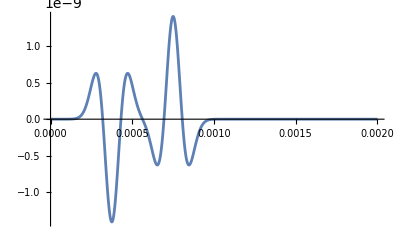

```mathematica
Plot[Sfap[0.00001,t,0.001,1000,0.015,0.03,.05, 5*10^-5,4*10^6],{t,0,0.002},PlotRange->All]
```

```mathematica
times = Subdivide[0,0.002,2000];
```

```mathematica
capValsSeparate = Table[Sfap[0.00001,t,0.001,1000,0.015,0.03,.05, 5*10^-5,4*10^6], {t,times}];
```

```mathematica
capValsTogether = Table[Sfap[0.00001,t,0.001,1000,0.015,0.02,.05, 5*10^-5,4*10^6], {t,times}];
```

General::munfl: 1.×10^-10 1.60057×10^-298 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.×10^-10 6.27531×10^-299 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.×10^-10 2.45877×10^-299 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
Export["~/Documents/ReciprocityStuff/NANS/FENS/capMyelinSeparate.dat",capValsSeparate]
```

~/Documents/ReciprocityStuff/NANS/FENS/capMyelinSeparate.dat

```mathematica
Export["~/Documents/ReciprocityStuff/NANS/FENS/capMyelinTogether.dat",capValsTogether]
```

~/Documents/ReciprocityStuff/NANS/FENS/capMyelinTogether.dat